# Lab 7: Trajectories and Moving Objects

## Computer Graphics Lab, Wolfram Mathematica

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->True]
SetOptions[{Plot,Plot3D,ContourPlot,ContourPlot3D,DensityPlot,ParametricPlot3D,ParametricPlot,ListPlot,ListLinePlot,ListPointPlot3D,Graphics,Graphics3D,PolarPlot},ImageSize->Small,AxesLabel->{"x","y","z"}];
```

```mathematica
(* Problem 1.1 *)
```

```mathematica
ListN01={1,2,-5,8,10,22,-5,-9,28,5,6,12,17}
```

{1,2,-5,8,10,22,-5,-9,28,5,6,12,17}

```mathematica
ListN02={1,1,1,1,1,-2,-5,-9,-28,-5,-6,-12,10}
```

{1,1,1,1,1,-2,-5,-9,-28,-5,-6,-12,10}

```mathematica
PosN[L_]:=Module[{S,i,T},
T=Table[If[L[[i]]>0,L[[i]],Nothing],{i,Length[L]}];
S=Sum[T[[i]],{i,Length[T]}];
S]
```

```mathematica
PosN[ListN01]
```

111

```mathematica
PosN[ListN02]
```

15

```mathematica
(* Problem 1.2 *)
```

```mathematica
ListN3={0,0,0,0,0,0,1,1,0,1,0,0,2}
```

{0,0,0,0,0,0,1,1,0,1,0,0,2}

```mathematica
Aver1[L_]:=Module[{S1,i,T},
T=Table[If[L[[i]]!=0,1/L[[i]],Nothing],{i,Length[L]}];
S1=Sum[T[[i]],{i,Length[T]}];
{T,S1}]
```

```mathematica
Aver1[ListN3]
```

{{1,1,1,1/2},7/2}

```mathematica
(* Problem 2.1 *)
```

```mathematica
PrN1N2[N1_,N2_]:=Module[{T},
T=Table[If[PrimeQ[i],i,Nothing],{i,N1,N2,1}];
T]
```

```mathematica
LP=PrN1N2[10,50]
```

{11,13,17,19,23,29,31,37,41,43,47}

```mathematica
PrN1N2Plot[N1_,N2_]:=Module[{i,plot,T},
T=Table[If[PrimeQ[i],i,Nothing],{i,N1,N2,1}];
plot=ListPlot[T,PlotStyle->{Red,PointSize[0.015]}];
{T,plot}]
```

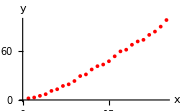
{{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97},-Graphics-}

```mathematica
PrN1N2Plot[1,100]
```

```mathematica
PrN1N2Bar[N1_,N2_]:=Module[{i,plot,T},
T=Table[If[PrimeQ[i],i,Nothing],{i,N1,N2,1}];
plot=BarChart[T];
{T,plot}]
```

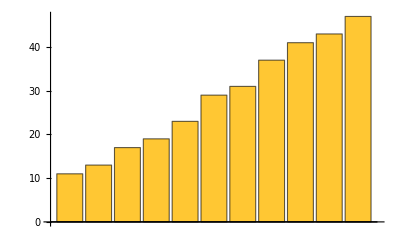
{{11,13,17,19,23,29,31,37,41,43,47},-Graphics-}

```mathematica
PrN1N2Bar[10,50]
```

```mathematica
(* Plot 2.2 *)
```

```mathematica
fN[k_]:=Module[{i,T},
T=Table[If[PrimeQ[i],i,Nothing],{i,1,k,1}];
Length[T]]
```

```mathematica
fN[50]
```

15

```mathematica
LN=Table[{i,fN[i]},{i,1,100}]
```

{{1,0},{2,1},{3,2},{4,2},{5,3},{6,3},{7,4},{8,4},{9,4},{10,4},{11,5},{12,5},{13,6},{14,6},{15,6},{16,6},{17,7},{18,7},{19,8},{20,8},{21,8},{22,8},{23,9},{24,9},{25,9},{26,9},{27,9},{28,9},{29,10},{30,10},{31,11},{32,11},{33,11},{34,11},{35,11},{36,11},{37,12},{38,12},{39,12},{40,12},{41,13},{42,13},{43,14},{44,14},{45,14},{46,14},{47,15},{48,15},{49,15},{50,15},{51,15},{52,15},{53,16},{54,16},{55,16},{56,16},{57,16},{58,16},{59,17},{60,17},{61,18},{62,18},{63,18},{64,18},{65,18},{66,18},{67,19},{68,19},{69,19},{70,19},{71,20},{72,20},{73,21},{74,21},{75,21},{76,21},{77,21},{78,21},{79,22},{80,22},{81,22},{82,22},{83,23},{84,23},{85,23},{86,23},{87,23},{88,23},{89,24},{90,24},{91,24},{92,24},{93,24},{94,24},{95,24},{96,24},{97,25},{98,25},{99,25},{100,25}}

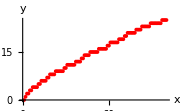

```mathematica
GfN=ListPlot[LN,PlotStyle->{Red,PointSize[0.015]}]
```

```mathematica
InT=LN[[{1,25,50,75,100}]]
```

{{1,0},{25,9},{50,15},{75,21},{100,25}}

```mathematica
fQint=Interpolation[InT,Method->"Spline"]
```

InterpolatingFunction[…]

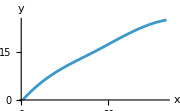

```mathematica
GF=Plot[fQint[t],{t,1,100}]
```

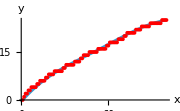

```mathematica
Show[{GF,GfN}]
```

```mathematica
(* Problem 3 *)
```

```mathematica
R1=3
```

3

```mathematica
f1[t_]:={R1*Cos[t],R1*Sin[t]+R1}
f2[t_]:={t,R1}
Tr1[t_]:=If[t>=0 && t<=2*Pi,f1[t],f2[t]]
```

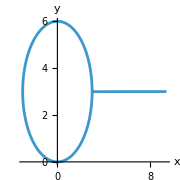

```mathematica
ParametricPlot[Tr1[t],{t,0,3Pi},Exclusions->None]
```

```mathematica
F[x_]:=Which[x>0,1,x<0,2,x==0,3]
```

```mathematica
F[1]
```

1

```mathematica
F[-2]
```

2

```mathematica
F[0]
```

3

```mathematica
F[x_]:=Which[x<0,f1[x],x<=5&&x>=0,f1[x],x>5,f1[x]]
```

```mathematica
F[1]
```

{3 Cos[1],3+3 Sin[1]}

```mathematica
(* Problem 4 *)
```

```mathematica
Clear[t,f1,f2,f3,Tra5,Tri5]
```

```mathematica
R11=3;
```

```mathematica
f1[t_]:={R11*Cos[t],R11*Sin[t]+R11} 
f2[t_]:={t,R11}
f3[t_]:={R11*Cos[t]+R11+3*Pi,R11*Sin[t]+R11}
```

```mathematica
Tra5[t_]:=Which[t>=0&&t<=2*Pi,f1[t],t>2*Pi&&t<3*Pi,f2[t],t>=3*Pi,f3[t]]
```

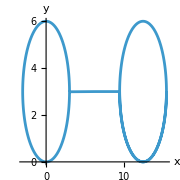

```mathematica
ff=ParametricPlot[Tra5[t],{t,0,6*Pi},Exclusions->None]
```

```mathematica
(* Problem 5 *)
```

```mathematica
Tri5[t_]:=Graphics[{Red,Disk[Tra5[t],1/2]},Axes->True]
```

```mathematica
ShowAll[t_]:=Show[Tri5[t],ff]
```

```mathematica
Manipulate[ShowAll[t],{t,0,6*Pi}]
```

```mathematica
(* Problem 6 *)
```

```mathematica
Ladder={{1,1},{5,5},{9,9},{13,13},{17,17},{21,21},{24,21},{28,17},{32,13},{36,9},{40,5}}
```

{{1,1},{5,5},{9,9},{13,13},{17,17},{21,21},{24,21},{28,17},{32,13},{36,9},{40,5}}

```mathematica
tmax=Max[Transpose[Ladder][[1]]]
```

40

```mathematica
fLadder=Interpolation[Ladder,InterpolationOrder->0]
```

InterpolatingFunction[…]

```mathematica
fL5[t_]:={t,fLadder[t]}
```

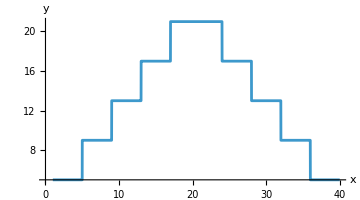

```mathematica
Tra15=ParametricPlot[fL5[t],{t,1,tmax},ImageSize->Medium]
```

```mathematica
nreg=3;RR5=5;
```

```mathematica
ObjectPol[s_]:={Red,RegularPolygon[fL5[s],RR5,nreg]}
```

```mathematica
Tri[s_]:=Graphics[ObjectPol[s]]
```

```mathematica
ShowAll2[s_]:=Show[{Tri[s],Tra15}]
```

```mathematica
Manipulate[ShowAll2[t],{t,1,tmax}]
```

```mathematica
(* Problem 7 *)
```

```mathematica
M7[nreg_,Rreg_]:=Module[{ObjectPol,GP,ShowAll5,s},
ObjectPol[s_]:={Red,RegularPolygon[fL5[s],RR5,nreg]};
GP[s_]:=Graphics[ObjectPol[s]];
ShowAll5[t_]:=Show[{Tra15,GP[t]}];
ShowAll5]
```

```mathematica
f7=M7[4,2]
```

ShowAll5$11194

```mathematica
Manipulate[f7[t],{t,1,tmax}]
```

```mathematica
(* Problem 8 *)
```

```mathematica
Clear[GPnew,GGPnew]
```

```mathematica
ObjectNew={Red,RegularPolygon[{0,0},RR5,nreg]}
```

{RGBColor[1, 0, 0],RegularPolygon[{0,0},5,3]}

```mathematica
ObjectRot[a_,s_]:=GeometricTransformation[ObjectNew,Composition[TranslationTransform[fL5[s]],RotationTransform[a]]]
```

```mathematica
GPnew[a_,s_]:=Graphics[ObjectRot[a,s],PlotRange->{{0,40},{-10,30}},Axes->True]
```

```mathematica
GGPnew[a_,s_]:=Show[GPnew[a,s],Tra15]
```

```mathematica
Manipulate[GGPnew[s,s],{s,1,tmax}]
```

```mathematica
(* Problem 9 *)
```

```mathematica
data9={{6.25,0.0},{6.001765667929582,0.4991670832341408},{5.278004317051997,0.9933466539753061},{4.13971935999042,1.477601033306698},{2.6826721590673235,1.9470917115432527},{1.0290638906736893,2.397127693021015},{-0.6830632803695947,2.823212366975177},{-2.3117715943739867,3.2210884361884555},{-3.7234679805828397,3.586780454497614},{-4.804363328451665,3.916634548137417},{-5.4701460286861545,4.207354924039483},{-5.6730252461135064,4.456036800307177},{-5.4055342260972905,4.660195429836132},{-4.700772462711884,4.817790927085965},{-3.62908203253932,4.927248649942301},{-2.2914696179044554,4.987474933020272},{-0.810373552546205,4.997868015207525},{0.6813909728405793,4.958324052262343},{2.05251635929549,4.869238154390976},{3.1848542843027783,4.731500438437072},{3.983796907172315,4.546487134128409},{4.386467155241201,4.316046833244369},{4.366996872319622,4.0424820190979505},{3.938434841957967,3.7285260608836},{3.1511303019605785,3.377315902755753},{2.087754321004162,2.992360720519782},{0.8554229419387158,2.577506859107321},{-0.42435467375067093,2.136899401169149},{-1.6269859224456151,1.6749407507795233},{-2.63633383181035,1.19624664606991},{-3.3554384511104276,0.7056000402993361},{-3.715449005983995,0.20790331216645247},{-3.681958130522893,-0.2918707171379004},{-3.258165023178643,-0.7887284707162433},{-2.4845813971987143,-1.2777055101341583},{-1.435306822050832,-1.7539161384480992},{-0.21121038911135578,-2.2126022164742625},{1.0693642937964811,-2.649180704542467},{2.281529134967273,-3.0592894547135963},{3.3054259689726977,-3.4388307959198707},{4.037394751401694,-3.7840124765396412},{4.399719513203253,-4.091385555322054},{4.348062109859167,-4.357878862067941},{3.8759001316492907,-4.580829683747274},{3.0155535206251787,-4.758010369447581},{1.8356904891936137,-4.887650588325485},{0.43551986299002976,-4.968455018167322},{-1.0638243785898849,-4.999616287820504},{-2.529946600811446,-4.9808230441792025},{-3.8309547730765376,-4.912263063121662},{-4.847278975639672,-4.794621373315692},{-5.482485967105465,-4.629073411638661},{-5.672118447703113,-4.417273278600765},{-5.389760456496705,-4.161337211119504},{-4.649774834880334,-3.8638224377799357},{-3.5064531650285042,-3.5277016278519597},{-2.0496368572833727,-3.1563331893616042},{-0.39718177268071464,-2.753427712988188},{1.3150800368523572,-2.323010897068783},{2.9450042957329634,-1.8693833241511801},{4.3564009896360165,-1.3970774909946293},{5.4308248157476635,-0.9108125213604751},{6.07785134254383,-0.41544701408748197}};
```

```mathematica
data91=Join[data9,{data9[[1]]}]
```

{{6.25,0.},{6.00177,0.499167},{5.278,0.993347},{4.13972,1.4776},{2.68267,1.94709},{1.02906,2.39713},{-0.683063,2.82321},{-2.31177,3.22109},{-3.72347,3.58678},{-4.80436,3.91663},{-5.47015,4.20735},{-5.67303,4.45604},{-5.40553,4.6602},{-4.70077,4.81779},{-3.62908,4.92725},{-2.29147,4.98747},{-0.810374,4.99787},{0.681391,4.95832},{2.05252,4.86924},{3.18485,4.7315},{3.9838,4.54649},{4.38647,4.31605},{4.367,4.04248},{3.93843,3.72853},{3.15113,3.37732},{2.08775,2.99236},{0.855423,2.57751},{-0.424355,2.1369},{-1.62699,1.67494},{-2.63633,1.19625},{-3.35544,0.7056},{-3.71545,0.207903},{-3.68196,-0.291871},{-3.25817,-0.788728},{-2.48458,-1.27771},{-1.43531,-1.75392},{-0.21121,-2.2126},{1.06936,-2.64918},{2.28153,-3.05929},{3.30543,-3.43883},{4.03739,-3.78401},{4.39972,-4.09139},{4.34806,-4.35788},{3.8759,-4.58083},{3.01555,-4.75801},{1.83569,-4.88765},{0.43552,-4.96846},{-1.06382,-4.99962},{-2.52995,-4.98082},{-3.83095,-4.91226},{-4.84728,-4.79462},{-5.48249,-4.62907},{-5.67212,-4.41727},{-5.38976,-4.16134},{-4.64977,-3.86382},{-3.50645,-3.5277},{-2.04964,-3.15633},{-0.397182,-2.75343},{1.31508,-2.32301},{2.945,-1.86938},{4.3564,-1.39708},{5.43082,-0.910813},{6.07785,-0.415447},{6.25,0.}}

```mathematica
x9=Transpose[data91][[1]]
```

{6.25,6.00177,5.278,4.13972,2.68267,1.02906,-0.683063,-2.31177,-3.72347,-4.80436,-5.47015,-5.67303,-5.40553,-4.70077,-3.62908,-2.29147,-0.810374,0.681391,2.05252,3.18485,3.9838,4.38647,4.367,3.93843,3.15113,2.08775,0.855423,-0.424355,-1.62699,-2.63633,-3.35544,-3.71545,-3.68196,-3.25817,-2.48458,-1.43531,-0.21121,1.06936,2.28153,3.30543,4.03739,4.39972,4.34806,3.8759,3.01555,1.83569,0.43552,-1.06382,-2.52995,-3.83095,-4.84728,-5.48249,-5.67212,-5.38976,-4.64977,-3.50645,-2.04964,-0.397182,1.31508,2.945,4.3564,5.43082,6.07785,6.25}

```mathematica
y9=Transpose[data91][[2]]
```

{0.,0.499167,0.993347,1.4776,1.94709,2.39713,2.82321,3.22109,3.58678,3.91663,4.20735,4.45604,4.6602,4.81779,4.92725,4.98747,4.99787,4.95832,4.86924,4.7315,4.54649,4.31605,4.04248,3.72853,3.37732,2.99236,2.57751,2.1369,1.67494,1.19625,0.7056,0.207903,-0.291871,-0.788728,-1.27771,-1.75392,-2.2126,-2.64918,-3.05929,-3.43883,-3.78401,-4.09139,-4.35788,-4.58083,-4.75801,-4.88765,-4.96846,-4.99962,-4.98082,-4.91226,-4.79462,-4.62907,-4.41727,-4.16134,-3.86382,-3.5277,-3.15633,-2.75343,-2.32301,-1.86938,-1.39708,-0.910813,-0.415447,0.}

```mathematica
L=Length[x9]
```

64

```mathematica
{fx9:=Interpolation[x9,Method->"Spline"],fy9:=Interpolation[y9,Method->"Spline"]}
```

{Null,Null}

```mathematica
A9[t_]:={fx9[t],fy9[t]}
```

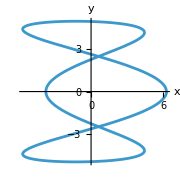

```mathematica
tra9=ParametricPlot[A9[t],{t,1,L}]
```

```mathematica
nreg
```

3

```mathematica
colorList=RandomColor[10]
```

{RGBColor[0.1545727480969623, 0.7611468708116547, 0.3806900279995493],RGBColor[0.4822292001543964, 0.21729934807959572, 0.7603465426694911],RGBColor[0.351481862517941, 0.669917882479053, 0.6674236204073305],RGBColor[0.9827586999921198, 0.2751675757586809, 0.7452871925337905],RGBColor[0.5651786435119976, 0.621838287522817, 0.6231608382228582],RGBColor[0.8032847601058324, 0.036575226337024036, 0.9593766407800108],RGBColor[0.0636629998436804, 0.7629794418801883, 0.9851044496924248],RGBColor[0.9427273236691724, 0.8899535797575919, 0.6698097932019518],RGBColor[0.00035062412526087883, 0.6479903664210303, 0.5229766397750537],RGBColor[0.6506033743127044, 0.7901654457865079, 0.5803849453556833]}

```mathematica
ObjectNew={Red,RegularPolygon[{0,0},RR5,nreg]}
```

{RGBColor[1, 0, 0],RegularPolygon[{0,0},5,3]}

```mathematica
ObjectRot[a_,s_]:=GeometricTransformation[ObjectNew,Composition[TranslationTransform[fL5[s]],RotationTransform[a]]]
```

```mathematica
GPnew[a_,s_]:=Graphics[ObjectRot[a,s],PlotRange->{{0,40},{-10,30}},Axes->True]
```

```mathematica
GGPnew[a_,s_]:=Show[GPnew[a,s],Tra15]
```

```mathematica
Manipulate[GGPnew[s,s],{s,1,tmax}]
```

```mathematica
Clear[ObjectNew9]
```

```mathematica
ObjectNew9[c_]:={c,RegularPolygon[{0,0},2,nreg]}
```

```mathematica
ObjectRot9[a_,s_,c_]:=GeometricTransformation[ObjectNew9[c],Composition[TranslationTransform[A9[s]],RotationTransform[a]]]
```

```mathematica
GPnew9[a_,s_,c_]:=Graphics[ObjectRot9[a,s,c],PlotRange->6,Axes->True]
```

```mathematica
ShowAll9[a_,s_,nreg_,C_]:=Show[{GPnew9[a,s,C],tra9}]
```

```mathematica
Manipulate[ShowAll9[a,s,nreg,C],{a,0,2*Pi},{s,1,L},{C,colorList}]
```

```mathematica
(* Problem 10 *)
```

```mathematica
Clear[S1,etraj1]
```

```mathematica
S1[u_,v_]:={u,v,u^2+v^2}
```

```mathematica
R1=2;
```

```mathematica
etraj1[t_]:={R1*Cos[5*t],R1*Sin[5*t],t}
```

```mathematica
MoveF0[F_,traj_,L0_]:=Module[{t1,plottraj,SurfacePosF,plotF1,plotF},
plottraj=ParametricPlot3D[traj[t1],{t1,0,L0}];
SurfacePosF[u_,v_,t1_]:=F[u,v]+traj[t1];
plotF[t1_]:=ParametricPlot3D[SurfacePosF[u,v,t1],{u,-1,1},{v,-1,1},Mesh->None];
plotF1[t1_]:=Show[{plotF[t1],plottraj},PlotRange->{{-2,2},{-2,2},{0,L0+1}}];
plotF1]
```

```mathematica
L0=7;
```

```mathematica
{M0=MoveF0[S1,etraj1,L0];Manipulate[M0[td],{td,0,L0}]}
```

{}

```mathematica
Manipulate[MoveF0[S1,etraj1,L0][td],{td,0,7}]
```

```mathematica
data10={{2.3511410091698925,-3.23606797749979,3},{3.804226065180614,1.2360679774997898,3},{0.,4.,3},{-3.804226065180614,1.2360679774997898,3},{-2.3511410091698925,-3.23606797749979,3},{-2.3511410091698925,-3.23606797749979,3}};
```

```mathematica
L10=Length[data10]
```

6

```mathematica
Interp3D[data_]:=Module[{x,y,z,fx,fy,fz},
x=Transpose[data][[1]];
y=Transpose[data][[2]];
z=Transpose[data][[3]];
fx=Interpolation[x];
fy=Interpolation[y];
fz=Interpolation[z];
traj={fx[#1],fy[#1],fz[#1]}&;
traj]
```

```mathematica
MoveF0New[F_,traj_,L0_]:=Module[{t1,plottraj,SurfacePosF,plotF1,plotF},
plottraj=ParametricPlot3D[traj[t1],{t1,1,L0}];
SurfacePosF[u_,v_,t1_]:=F[u,v]+traj[t1];
plotF[t1_]:=ParametricPlot3D[SurfacePosF[u,v,t1],{u,-1,1},{v,-1,1},Mesh->None];
plotF1[t1_]:=Show[{plotF[t1],plottraj},PlotRange->{{-4,4},{-4,4},{1,L0+1}}];
plotF1]
```

```mathematica
traj10=Interp3D[data10]
```

{fx$14150[#1],fy$14150[#1],fz$14150[#1]}&

```mathematica
M10=MoveF0New[S1,traj10,L10]
```

plotF1$14151

```mathematica
Manipulate[M10[td],{td,1,L10}]
```

```mathematica
(* Songkran 1 *)
```

```mathematica
Clear[S1]
```

```mathematica
S1[u_,v_]:={u,v,u^2+v^2}
```

```mathematica
R1=2;
```

```mathematica
etraj1[t_]:={R1*Cos[10*t],R1*Sin[10*t],t}
```

```mathematica
Moveff0[F_,traj_,L0_]:=Module[{t1,plottraj,SurfacePosF,plotpoints,plotF1,plotF},
plottraj=ParametricPlot3D[traj[t1],{t1,1,L0}];
SurfacePosF[u_,v_,t1_]:=F[u,v]+traj[t1];
plotF[t1_]:=ParametricPlot3D[SurfacePosF[u,v,t1],{u,-1,1},{v,-1,1},Mesh->None];
plotF1[t1_]:=Show[{plotF[t1],plottraj},PlotRange->{{-2,2},{-2,2},{0,L0+1}}];
plotF1]
```

```mathematica
(* Problem 1 *)
```

```mathematica
L0=7
```

7

```mathematica
MoveF1[F_,traj_,L0_,ColorS_,ColorT_]:=Module[{t1,plottraj,SurfacePosF,plotpoints,plotF1,plotF},
plottraj=ParametricPlot3D[traj[t1],{t1,1,L0},PlotStyle->ColorT];
SurfacePosF[u_,v_,t1_]:=F[u,v]+traj[t1];
plotF[t1_]:=ParametricPlot3D[SurfacePosF[u,v,t1],{u,-1,1},{v,-1,1},Mesh->None,PlotStyle->ColorS];
plotF1[t1_]:=Show[{plotF[t1],plottraj},PlotRange->{{-2,2},{-2,2},{0,L0+1}}];
plotF1]
```

```mathematica
M1=MoveF1[S1,etraj1,L0,Red,Purple]
```

plotF1$14643

```mathematica
Manipulate[M1[td],{td,0,L0,0.001}]
```

```mathematica
L0=4;ListT=RandomColor[8];ListS=RandomColor[8];
```

```mathematica
Manipulate[MoveF1[S1,etraj1,10,CS,CT][td],{td,0,L0},{CS,ListS},{CT,ListT}]
```

```mathematica
(* Problem 2 *)
```

```mathematica
L0=4;
```

```mathematica
MoveF2[F_,traj_,L0_,ColorS_,ColorT_,X_,Y_]:=Module[{t1,plottraj,SurfacePosF,plotpoints,plotF1,plotF},
plottraj=ParametricPlot3D[traj[t1],{t1,1,L0},PlotStyle->ColorT];
SurfacePosF[u_,v_,t1_]:=F[u,v]+traj[t1];
plotF[t1_]:=ParametricPlot3D[SurfacePosF[u,v,t1],{u,-1,1},{v,-1,1},Mesh->None,PlotStyle->ColorS];
plotF1[t1_]:=Show[{plotF[t1],plottraj},PlotRange->{{-X,X},{-Y,Y},{0,L0+1}}];
plotF1]
```

```mathematica
SL1={Slider2D[Dynamic[xy],{{1,1},{10,10}}],Dynamic[xy]}
```

{,}

```mathematica
SL2={VerticalSlider[Dynamic[L0],{2,8},Background->Pink],Dynamic[L0]}
```

{,}

```mathematica
{Manipulate[MoveF2[S1,etraj1,L0,CS,CT,xy[[1]],xy[[2]]][td],{td,0,L0},{CS,ListS},{CT,ListT}],SL1,SL2}
```

{,{,},{,}}

```mathematica
(* Problem 3 *)
```

```mathematica
R1=2;
```

```mathematica
etraj1[t_]:={R1*Cos[10*t],R1*Sin[10*t],t}
```

```mathematica
Movef0[F_,traj_,L0_]:=Module[{t1,plottraj,SurfacePosF,plotpoints,plotF1,plotF},
plottraj=ParametricPlot3D[traj[t1],{t1,1,L0}];
SurfacePosF[u_,v_,t1_]:=F[u,v]+traj[t1];
plotF[t1_]:=ParametricPlot3D[SurfacePosF[u,v,t1],{u,-1,1},{v,-1,1},Mesh->None];
plotF1[t1_]:=Show[{plotF[t1],plottraj},PlotRange->{{-2,2},{-2,2},{0,L0+1}}];
plotF1]
```

```mathematica
MoveF0[S1,etraj1,L0][1]
```

-Graphics3D-

```mathematica
MoveF3[F_,traj_,L0_,ColorS_,ColorT_,rr_]:=Module[{t1,plottraj,plotpoints,plotF1,plotF},
plottraj=ParametricPlot3D[traj[t1],{t1,1,L0},PlotStyle->ColorT];
plotF[t1_]:=Graphics3D[{ColorS,F[traj[t1],rr]}];
plotF1[t1_]:=Show[{plotF[t1],plottraj},PlotRange->{{-2,2},{-2,2},{0,L0+1}}];
plotF1]
```

```mathematica
Manipulate[MoveF3[Cube,etraj1,L0,Red,Blue,0.5][td],{td,0,L0}]
```

```mathematica
(* Problem 4 *)
```

```mathematica
Manipulate[MoveF3[Sphere,etraj1,L0,Red,Blue,0.5][td],{td,0,L0}]
```

```mathematica
LineR[P_,R_]:={Thickness[0.05],Line[{P-{0,0,R},P+{0,0,R}}]}
```

```mathematica
Graphics3D[LineR[{0,0,0},1]]
```

-Graphics3D-

```mathematica
Manipulate[MoveF3[LineR,etraj1,L0,Red,Green,0.5][td],{td,0,L0}]
```

```mathematica
(* Problem 5.1 *)
```

```mathematica
MoveF5[F_,traj_,L0_,ColorS_,ColorT_,R1_]:=Module[{t1,plottraj,plotpoints,plotF1,plotF,Object,RandomColor},
If[ColorS==ColorT,Return["Change the input colors"]];
plottraj=ParametricPlot3D[traj[t1],{t1,0,L0},PlotStyle->ColorT];
Object[t1_]:={ColorS,F[traj[t1],R1]};
plotF[t1_]:=Graphics3D[Object[t1],R1];
plotF1[t1_]:=Show[{plotF[t1],plottraj},PlotRange->{{-2,2},{-2,2},{0,L0+1}}];
plotF1]
```

```mathematica
MoveF5[Cube,etraj1,L0,Red,Red,1.5]
```

Change the input colors

```mathematica
RandomColor[1]
```

{RGBColor[0.842900972650267, 0.3048571607945425, 0.7665066045915336]}

```mathematica
{If[Red==Red,Blue,Red],F[traj[1],R1]}
```

{RGBColor[0, 0, 1],F[{2.35114,-3.23607,3},2]}

```mathematica
MoveF51[F_,traj_,L0_,ColorS_,ColorT_,R1_]:=Module[{plottraj,plotF1,plotF,Objectt,rc,rc1},
rc=Red;
rc1=Blue;
Objectt[t1_]:={If[ColorS==ColorT,rc=rc1,ColorS],F[traj[t1],R1]};
plottraj=ParametricPlot3D[traj[t1],{t1,0,L0},PlotStyle->rc];


plotF[t1_]:=Graphics3D[Objectt[t1]];
plotF1[t1_]:=Show[{plotF[t1],plottraj},PlotRange->{{-2,2},{-2,2},{0,L0+1}}];
plotF1]
```

```mathematica
Manipulate[MoveF51[LineR,etraj1,L0,Blue,Blue,R1][t],{t,1,L0}]
```

```mathematica
(* Problem 5.2 *)
```

```mathematica
R2=0.8
```

0.8

```mathematica
MoveF52[F_,traj_,L0_,ColorS_,ColorT_,R1_]:=Module[{t1,SurfacePosF,plottraj,plotpoints,plotF1,plotF,Object},
If[(!NumericQ[R1]||!NumericQ[L0]),Return["R1 or L0 are not connected"]];
plottraj=ParametricPlot3D[traj[t1],{t1,0,L0},PlotStyle->ColorT];
Object[t1_]:={rc,F[traj[t1],R1]};
plotF[t1_]:=Graphics3D[Object[t1]];
plotF1[t1_]:=Show[{plotF[t1],plottraj},PlotRange->{{-2,2},{-2,2},{0,L0+1}}];
plotF1]
```

```mathematica
MoveF52[Cube,etraj1,L0,Red,Blue,S]
```

R1 or L0 are not connected

```mathematica
MoveF52[Cube,etraj1,S,Red,Blue,S]
```

R1 or L0 are not connected

```mathematica
MoveF52[Cube,etraj1,L0,Red,Blue,R1][1]
```

-Graphics3D-

```mathematica
(* Problem 6 *)
```

```mathematica
Interp3D[data_]:=Module[{x,y,z,fx,fy,fz},
x=Transpose[data][[1]];
y=Transpose[data][[2]];
z=Transpose[data][[3]];
fx=Interpolation[x];
fy=Interpolation[y];
fz=Interpolation[z];
traj={fx[#1],fy[#1],fz[#1]}&;
traj]
```

```mathematica
data6={{-4,2,4},{4,5,-1},{2,5,0},{1,1,3},{2,-6,-6},{-4,-4,-4},{0,0,0},{0,0,0},{1,5,0},{1,1,3},{1,-1,-1},{2,2,2}};
```

```mathematica
L6=Dimensions[data6][[1]]
```

12

```mathematica
Interp3D[data6][1]
```

{-4,2,4}

```mathematica
MoveF6[F_,data_,ColorS_,ColorT_,R1_]:=Module[{t1,SurfacePosF,plottraj,plotpoints,plotF1,plotF,Object},
plottraj=ParametricPlot3D[Interp3D[data6][t1],{t1,1,L6},PlotStyle->ColorT];
Object[t1_]:={Red,F[traj[t1],R1]};
plotF[t1_]:=Graphics3D[Object[t1]];
plotF1[t1_]:=Show[{plotF[t1],plottraj},PlotRange->7];
plotF1]
```

```mathematica
Manipulate[MoveF6[Sphere,data6,Red,Blue,1.5][td],{td,1,L6}]
```